```mathematica
ClearAll["Global`*"]

(*This tutorial contains:-
1. Some simple Bezier Curves and how to Manipulate them
2. *)
```

```mathematica
(*The following are notes on Bezier Curve*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
(*The Following  are notes on BSplines*)
```

```mathematica
-Graphics--Graphics--Graphics-
(*The following are notes on Bspline emphasizing on how knot vectors are selected.*)
-Graphics-
```

## (*Bezier Curves*)

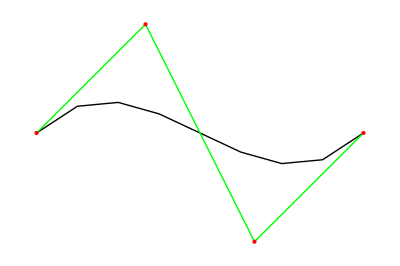

```mathematica
(*BezierCurve draws a composite Bézier curve that is defined by the given control points.By default,a cubic Bézier curve is used:*)
pts={{0,0},{1,1},{2,-1},{3,0}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

## (*Splines*)

```mathematica
(*Splines*)
pts=Table[{i,(-1)^i},{i,7}]
Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts]}]
```

{{1,-1},{2,1},{3,-1},{4,1},{5,-1},{6,1},{7,-1}}

-Graphics-

```mathematica
(*Testing Spline degrees*)
pts=Table[{i,(-1)^i},{i,7}]
Length[pts]
Table[Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineDegree->d]}],{d,1,6}]
Manipulate[Graphics[{Green,Line[pts],Red,Point[pts],Black,BSplineCurve[pts,SplineDegree->d]}],{d,1,10,1}]
```

{{1,-1},{2,1},{3,-1},{4,1},{5,-1},{6,1},{7,-1}}

7

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*BSpline Surfaces*)
cpts=Table[{i,j,RandomReal[{-1,1}]},{i,5},{j,5}]
Length[cpts];
b=Graphics3D[BSplineSurface[cpts]];
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,cpts],Gray,Line[cpts],Line[Transpose[cpts]]}],b]
```

{{{1,1,0.816289},{1,2,-0.970197},{1,3,0.0941414},{1,4,0.988186},{1,5,0.335945}},{{2,1,-0.650236},{2,2,0.151263},{2,3,-0.838217},{2,4,-0.651608},{2,5,-0.319601}},{{3,1,-0.22121},{3,2,-0.768048},{3,3,0.275111},{3,4,-0.139768},{3,5,0.373252}},{{4,1,0.327364},{4,2,0.710571},{4,3,0.418923},{4,4,0.93296},{4,5,0.399883}},{{5,1,-0.602668},{5,2,0.00108288},{5,3,-0.923657},{5,4,0.971612},{5,5,-0.506936}}}

-Graphics3D-

```mathematica
(*Bspilne Surfaces*)
pts=Table[{Cos[2 Pi u/6] Cos[v],Sin[2 Pi u/6] Cos[v],v},{u,6},{v,-1,1,1/2}];
f=BSplineFunction[pts,SplineClosed->{True,False}]
Show[Graphics3D[{PointSize[Medium],Red,Map[Point,pts]}],Graphics3D[{Gray,Line[pts],Gray,Line[Transpose[pts]]}],ParametricPlot3D[f[u,v],{u,0,1},{v,0,1}]]
```

BSplineFunction[…]

-Graphics3D-

```mathematica
(*3x4 array of control points where the height of the points can be manipulated*)
Pts0[z11_,z12_,z13_,z21_,z22_,z23_,z31_,z32_,z33_,z41_,z42_,z43_]:={{z11,z12,z13},{z21,z22,z23},{z31,z32,z33},{z41,z42,z43}}
Pts1[z11_,z12_,z13_,z21_,z22_,z23_,z31_,z32_,z33_,z41_,z42_,z43_]:=Table[{i,j,Pts0[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43][[i]][[j]]},{i,1,4},{j,1,3}]
ff[z11_,z12_,z13_,z21_,z22_,z23_,z31_,z32_,z33_,z41_,z42_,z43_]:=BSplineFunction[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43],SplineClosed->{True,False}]
(*Manipulate[Graphics3D[BSplineSurface[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]],PlotRange->{{1,4},{1,3},{0,5}}],{z11,0,5},{z12,0,5},{z13,0,5},{z21,0,5},{z22,0,5},{z23,0,5},{z31,0,5},{z32,0,5},{z33,0,5},{z41,0,5},{z42,0,5},{z43,0,5}]
*)Manipulate[Graphics3D[{PointSize[Medium],Red,Map[Point,Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]],Gray,Line[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]],Line[Transpose[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]]],BSplineSurface[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]]},PlotRange->{{1,4},{1,3},{0,5}}],{z11,0,5},{z12,0,5},{z13,0,5},{z21,0,5},{z22,0,5},{z23,0,5},{z31,0,5},{z32,0,5},{z33,0,5},{z41,0,5},{z42,0,5},{z43,0,5}]
(*Manipulate[Show[Graphics3D[{PointSize[Medium],Red,Map[Point,Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]]}],Graphics3D[{Gray,Line[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]],Gray,Line[Transpose[Pts1[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43]]]}],ParametricPlot3D[ff[z11,z12,z13,z21,z22,z23,z31,z32,z33,z41,z42,z43][u,v],{u,1,3},{v,1,4}]],{z11,0,5},{z12,0,5},{z13,0,5},{z21,0,5},{z22,0,5},{z23,0,5},{z31,0,5},{z32,0,5},{z33,0,5},{z41,0,5},{z42,0,5},{z43,0,5}]*)
```

```mathematica
(*Means to manipulate 8 control point sof  a BSpilen surface*)
Manipulate[cpts={{pt1,pt2,pt3,pt4},{pt5,pt6,pt7,pt8}}(*defines the control point*);
Graphics3D[{BSplineSurface[cpts](*Std Bspline surface command*),RGBColor[.1,.73,.36](*controls color of the markers*),PointSize[.05](*size of the markert*),Point[Flatten[cpts,1]](*Std Point command to plot control point*),Black(*Color of text in the marker*),If[labels,{Text[1,pt1],Text[2,pt2],Text[3,pt3],Text[4,pt4],Text[5,pt5],Text[6,pt6],Text[7,pt7],Text[8,pt8]},{}](*puts text on each of the control points*)},ImageSize->{400,400}(*controls the domension of the manipulate box*),PlotRange->1(*equiv to (-1,1)^3 as the domain*)],{{pt,1,"select control point"},{1,2,3,4,5,6,7,8}}(*This is the control to pick a specific control point. That value is the value of the variable pt.*),{{labels,True},{True,False}},PaneSelector[{1->Control[{{pt1(*u*),{0,0,0}(*initial val of pt1*),"xyz"},{-1,-1,-1},{1,1,1}(*domain of point 1*)}],2->Control[{{pt2,{-0.3,0.8,0.9},"xyz"},{-1,-1,-1},{1,1,1}}],3->Control[{{pt3,{-0.2,0,0.6},"xyz"},{-1,-1,-1},{1,1,1}}],4->Control[{{pt4,{0.3,0.7,-0.7},"xyz"},{-1,-1,-1},{1,1,1}}],5->Control[{{pt5,{-0.4,0.9,-0.1},"xyz"},{-1,-1,-1},{1,1,1}}],6->Control[{{pt6,{-0.4,-0.8,0.7},"xyz"},{-1,-1,-1},{1,1,1}}],7->Control[{{pt7,{0.4,-0.1,0.2},"xyz"},{-1,-1,-1},{1,1,1}}],8->Control[{{pt8,{0,-0.4,-0.5},"xyz"},{-1,-1,-1},{1,1,1}}]},Dynamic[pt]],TrackedSymbols->True,AutorunSequencing->{2,3}]
```

{{0,1},{1/7,-1},{2/7,1},{3/7,-1},{4/7,1},{5/7,-1},{6/7,1},{1,-1}}

-Graphics-

-Graphics-

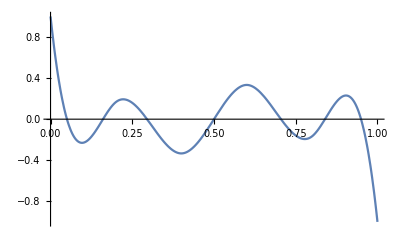

```mathematica
(*Obtaining a Parametric expression for the Bspline curve.*)
Nn=7;
pts1=Table[{i/Nn,(-1)^i},{i,0,Nn}](*Everything has been set between [0,1] for simplicity.*)
d=3;
Knots1=Subdivide[0,1,d+Nn+1];
For[i=1,i<=Length[Knots1],i++,If[i<=d+1,Knots1[[i]]=0,{}];If[i>=Length[Knots1]-d,Knots1[[i]]=1,{}];If[i>=d+2&&i<=Length[Knots1]-d-1,Knots1[[i]]=(i-d-1)/(Nn-d+1),{}]];
Knots1;(*Generate a knot vector with first d+1 entries=0 last d+1 entries=1 and middle entries equally spaced*)
cx[t_]:=Sum[pts1[[i,1]]*BSplineBasis[{d,Knots1},i-1,t],{i,Nn+1}]
cy[t_]:=Sum[pts1[[i,2]]*BSplineBasis[{d,Knots1},i-1,t],{i,Nn+1}]
p1= Graphics[BSplineCurve[pts1,SplineDegree->d]];
p2=ParametricPlot[{cx[t],cy[t]},{t,0,1},PlotStyle->{Dashed,Thickness[0.02]}];
Show[{p1,p2}]
Graphics[{ BSplineCurve[pts1,SplineDegree->d],Green,Line[pts1],Red,Point[pts1]}]
Plot[cy[t],{t,0,1}]
```

```mathematica
(*Trying to get the Functional form from the parameteric equations*)
cx1[t_]:=Sum[pts1[[i,1]]*BSplineBasis[{d,Knots1},i-1,t],{i,Nn+1}];
cy1[t_]:=Sum[pts1[[i,2]]*BSplineBasis[{d,Knots1},i-1,t],{i,Nn+1}];
(*Soln=Solve[Sum[pts1[[i,1]]*BSplineBasis[{d,Knots1},i-1,t],{i,Nn+1}]==x1&&0<=t<=1,t,Reals] 
u[x1_]:=x/.Soln*)
soul=(t/. Solve[cx1[t]==x,t])
(*Plot[cy1[t]/. Solve[cx1[t]==x,t],{x,0,1}]*)
(*Cyx[x_]:=cy1[InverseFunction[Function[{a},cx1[a]]][x]];
Cyx[x];
Plot[Cyx[x],{x,0,1},AspectRatio->Automatic]*)
```

t

```mathematica
(*Obtaining a Parametric expression for the Bspline surface.*)
Nnx=7;(*There are Nnx+1 points in this direction*)
Nny=7;(*There are Nny+1 points in this direction*)
pts2=Table[{i/Nnx,j/Nny,(i/Nnx)^2*(j/Nny)^2},{i,0,Nnx},{j,0,Nny}];(*The z value will be chosen according to the function x^2 y^2*)
dx=3;
dy=3;
Knotsx1=Subdivide[0,1,dx+Nnx+1];
Knotsy1=Subdivide[0,1,dy+Nny+1];
For[i=1,i<=Length[Knotsx1],i++,If[i<=dx+1,Knotsx1[[i]]=0,{}];If[i>=Length[Knotsx1]-dx,Knotsx1[[i]]=1,{}];If[i>=dx+2&&i<=Length[Knotsx1]-dx-1,Knotsx1[[i]]=(i-dx-1)/(Nnx-dx+1),{}]];
For[i=1,i<=Length[Knotsy1],i++,If[i<=dy+1,Knotsy1[[i]]=0,{}];If[i>=Length[Knotsy1]-dx,Knotsy1[[i]]=1,{}];If[i>=dy+2&&i<=Length[Knotsy1]-dy-1,Knotsy1[[i]]=(i-dy-1)/(Nny-dy+1),{}]];
Knotsx1;
Knotsy1;
cx[u_,v_]:=Sum[pts2[[i,j,1]]*BSplineBasis[{dx,Knotsx1},i-1,u]*BSplineBasis[{dy,Knotsy1},j-1,v],{i,Nnx+1},{j,Nny+1}]
cy[u_,v_]:=Sum[pts2[[i,j,2]]*BSplineBasis[{dx,Knotsx1},i-1,u]*BSplineBasis[{dy,Knotsy1},j-1,v],{i,Nnx+1},{j,Nny+1}]
cz[u_,v_]:=Sum[pts2[[i,j,3]]*BSplineBasis[{dx,Knotsx1},i-1,u]*BSplineBasis[{dy,Knotsy1},j-1,v],{i,Nnx+1},{j,Nny+1}]
p1=Graphics3D[BSplineSurface[pts2]];
p2=ParametricPlot3D[{cx[u,v],cy[u,v],cz[u,v]},{u,0,1},{v,0,1},PlotRange->{0,1},PlotStyle->{Directive[Yellow,Specularity[White,20],Opacity[0.8]],Thickness[0.01]}]
Show[{p1,p2}]
Plot3D[{cx[u,v],cy[u,v]},{u,0,1},{v,0,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-